# Pango analysis: Plotting partitioned case counts and Rt

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/trvrb/Documents/src/rt-from-frequency-dynamics/results/pango-countries

## Setup

### Parameters

```mathematica
dataset="pango-countries";
```

```mathematica
model="GARW";
```

```mathematica
imageSize=300;
```

```mathematica
gridCount=1;
```

```mathematica
rtMax=1.6;
```

```mathematica
rtMin=0.6;
```

### Date ticks

```mathematica
dateTicks={"2022-03-01","2022-04-01","2022-05-01","2022-06-01","2022-07-01","2022-08-01","2022-09-01","2022-10-01","2022-11-01","2022-12-01","2023-01-01","2023-02-01","2023-03-01"};
```

### Countries

```mathematica
countriesToDrop={};
```

## Variants and colors

### Import

```mathematica
variantData=Import["../../estimates/"<>dataset<>"/"<>dataset<>"_Rt-combined-"<>model<>".tsv"];
```

```mathematica
header=variantData[[1]]
```

{date,location,variant,median_R,R_upper_95,R_lower_95,R_upper_80,R_lower_80,R_upper_50,R_lower_50,median_freq}

```mathematica
headerRules=MapIndexed[#1->#2[[1]]&,header]
```

{date→1,location→2,variant→3,median_R→4,R_upper_95→5,R_lower_95→6,R_upper_80→7,R_lower_80→8,R_upper_50→9,R_lower_50→10,median_freq→11}

```mathematica
variantData=Drop[variantData,1];
```

```mathematica
variants=Union[variantData[[All,3]]]
```

{BA,BA.2.3.20,BA.2.75,BA.2.75.2,BA.2.75.4,BA.4.6,BA.4.6.5,BA.5,BA.5.1,BA.5.1.1,BA.5.1.10,BA.5.1.12,BA.5.1.18,BA.5.1.22,BA.5.1.23,BA.5.1.25,BA.5.1.27,BA.5.1.30,BA.5.1.5,BA.5.1.6,BA.5.2,BA.5.2.1,BA.5.2.13,BA.5.2.14,BA.5.2.20,BA.5.2.21,BA.5.2.23,BA.5.2.31,BA.5.2.34,BA.5.2.35,BA.5.2.57,BA.5.2.59,BA.5.2.6,BA.5.2.9,BA.5.3,BA.5.3.1,BA.5.5,BA.5.5.1,BA.5.6,BA.5.9,BE.1,BE.10,BE.1.1,BE.1.1.1,BE.1.2,BE.1.2.1,BE.1.4.2,BE.4.2,BE.9,BF.10,BF.11,BF.13,BF.14,BF.25,BF.26,BF.27,BF.32,BF.5,BF.7,BF.7.4,BF.7.4.1,BF.7.5,BF.7.6,BK.1,BM.1.1,BN.1,BN.1.2,BN.1.3,BN.1.3.1,BN.1.3.6,BN.1.4,BN.1.5,BN.1.7,BQ.1,BQ.1.1,BQ.1.10,BQ.1.10.1,BQ.1.1.1,BQ.1.11,BQ.1.1.10,BQ.1.1.13,BQ.1.1.15,BQ.1.1.18,BQ.1.1.2,BQ.1.12,BQ.1.1.23,BQ.1.1.27,BQ.1.1.28,BQ.1.1.3,BQ.1.13,BQ.1.13.1,BQ.1.1.32,BQ.1.1.35,BQ.1.1.4,BQ.1.14,BQ.1.1.40,BQ.1.1.41,BQ.1.1.43,BQ.1.1.5,BQ.1.15,BQ.1.1.51,BQ.1.1.52,BQ.1.1.54,BQ.1.1.57,BQ.1.1.6,BQ.1.1.63,BQ.1.1.65,BQ.1.1.67,BQ.1.1.68,BQ.1.1.69,BQ.1.1.7,BQ.1.18,BQ.1.2,BQ.1.22,BQ.1.23,BQ.1.25,BQ.1.25.1,BQ.1.27,BQ.1.28,BQ.1.3,BQ.1.31,BQ.1.5,BQ.1.6,BQ.1.8,BR.2.1,BU.1,BW.1,BW.1.1,CA.3.1,CH.1.1,CH.1.1.1,CK.1,CK.2.1,CK.2.1.1,CL.1,CM.2,CM.8.1,CN.2,CP.1,CQ.2,CR.1.1,CZ.2,DF.1.1,DR.1,DT.2,EB.1,ED.2,EE.1,EE.2,EE.5,EF.1,EF.1.1,other,XBB,XBB.1,XBB.1.15,XBB.1.5,XBB.1.5.1,XBB.1.5.11,XBB.1.5.13,XBB.1.5.4,XBB.1.5.7,XBB.1.5.9,XBB.1.9,XBB.2,XBF}

```mathematica
n=Length[variants]
```

166

### Max frequency

```mathematica
variantFrequencyMapping=Table[variant->Max[Cases[variantData,x_/;x[[3]]==variant][[All,11]]],{variant,variants}];
```

```mathematica
highFrequencyVariants=Cases[variantFrequencyMapping,x_/;x[[2]]>=0.005][[All,1]];
```

```mathematica
Length[highFrequencyVariants]
```

67

```mathematica
lowFrequencyVariants=Complement[variants,highFrequencyVariants];
```

```mathematica
Length[lowFrequencyVariants]
```

99

```mathematica
variants=Join[highFrequencyVariants,lowFrequencyVariants];
```

```mathematica
n=Length[variants]
```

166

### Variant to clade mapping and clade colors

```mathematica
toHexString[n_Integer]:=StringJoin[ToString/@(IntegerDigits[n,16]/.Thread[Range[10,15]->CharacterRange["A","F"]])]
```

```mathematica
rgbColorToHex[rgbColor_]:="#"<>StringJoin[Map[toHexString[Round[#*255]]&,Level[rgbColor,1]]]
```

```mathematica
start[n_]:=0.05;
```

```mathematica
stop[n_]:=0.99;
```

```mathematica
gap[n_]:=(stop[n]-start[n])/(n-1)
```

```mathematica
makeColors[n_]:=Table[ColorData["Rainbow"][i],{i,start[n],stop[n],gap[n]}];
```

```mathematica
startGrays[n_]:=0.35;
```

```mathematica
stopGrays[n_]:=0.65;
```

```mathematica
gapGrays[n_]:=(stopGrays[n]-startGrays[n])/(n-1)
```

```mathematica
makeGrays[n_]:=Table[GrayLevel[i],{i,startGrays[n],stopGrays[n],gapGrays[n]}];
```

```mathematica
variantToClade=Map[#[[1]]->#[[2]]&,Drop[Import["../../data/pango-countries/pango_aliasing.tsv","Table","Numeric"->False],1]];
```

```mathematica
clades={"other","21L","22A","22B","22C","22D","22E","22F","23A"};
```

```mathematica
cladeColors=Prepend[makeColors[Length[clades]-1],Gray]
```

{GrayLevel[0.5],RGBColor[0.3431304, 0.11581720000000001, 0.6369784000000001],RGBColor[0.24442189714285714, 0.35425512, 0.8136703542857143],RGBColor[0.3112192114285714, 0.5923928742857142, 0.7305370971428573],RGBColor[0.4503775714285713, 0.7087464457142857, 0.5158382742857144],RGBColor[0.6460493028571428, 0.74327364, 0.33515914857142864],RGBColor[0.831986057142857, 0.6938050571428572, 0.24765657142857148],RGBColor[0.9022855371428572, 0.49372713142857155, 0.19958264000000003],RGBColor[0.86067868, 0.15704232000000032, 0.13666448000000006]}

```mathematica
cladeToColor=MapThread[#1->#2&,{clades,cladeColors}]
```

{other→GrayLevel[0.5],21L→RGBColor[0.3431304, 0.11581720000000001, 0.6369784000000001],22A→RGBColor[0.24442189714285714, 0.35425512, 0.8136703542857143],22B→RGBColor[0.3112192114285714, 0.5923928742857142, 0.7305370971428573],22C→RGBColor[0.4503775714285713, 0.7087464457142857, 0.5158382742857144],22D→RGBColor[0.6460493028571428, 0.74327364, 0.33515914857142864],22E→RGBColor[0.831986057142857, 0.6938050571428572, 0.24765657142857148],22F→RGBColor[0.9022855371428572, 0.49372713142857155, 0.19958264000000003],23A→RGBColor[0.86067868, 0.15704232000000032, 0.13666448000000006]}

### Colors

```mathematica
colorMappingForClade[clade_]:=Module[{pos,shades,tints,col},
pos=Flatten[Position[variants,x_/;(x/.variantToClade)==clade]];
If[Length[pos]>0,
shades=Reverse[Table[Darker[clade/.cladeToColor,x],{x,0,0.5,1/(Length[pos])}]];
tints=Drop[Table[Lighter[clade/.cladeToColor,x],{x,0,0.5,1/(Length[pos])}],1];
col=Join[shades,tints];
Table[variants[[pos[[i]]]]->col[[i]],{i,Length[pos]}],
{}
]
]
```

```mathematica
variantColorMapping=Flatten[Map[colorMappingForClade,clades]]
```

{other→RGBColor[0.5, 0.5, 0.5],BA.2.3.20→RGBColor[0.2287536, 0.07721146666666667, 0.4246522666666667],CM.2→RGBColor[0.3431304, 0.11581720000000001, 0.6369784000000001],CM.8.1→RGBColor[0.5620869333333334, 0.4105448, 0.7579856],BA.4.6→RGBColor[0.12221094857142857, 0.17712756, 0.40683517714285716],BA.4.6.5→RGBColor[0.24442189714285714, 0.35425512, 0.8136703542857143],BA.5→RGBColor[0.1556096057142857, 0.2961964371428571, 0.36526854857142865],BA.5.1→RGBColor[0.16005559444897957, 0.3046591924897959, 0.3757047928163266],BA.5.1.10→RGBColor[0.16450158318367344, 0.31312194783673464, 0.3861410370612246],BA.5.1.27→RGBColor[0.16894757191836735, 0.32158470318367344, 0.3965772813061226],BA.5.1.30→RGBColor[0.17339356065306122, 0.3300474585306122, 0.4070135255510205],BA.5.2→RGBColor[0.1778395493877551, 0.338510213877551, 0.41744976979591847],BA.5.2.1→RGBColor[0.18228553812244896, 0.3469729692244897, 0.4278860140408164],BA.5.2.20→RGBColor[0.18673152685714284, 0.35543572457142847, 0.43832225828571436],BA.5.2.23→RGBColor[0.1911775155918367, 0.36389847991836727, 0.44875850253061234],BA.5.2.34→RGBColor[0.19562350432653058, 0.37236123526530607, 0.4591947467755103],BA.5.2.6→RGBColor[0.20006949306122446, 0.3808239906122448, 0.4696309910204083],BA.5.2.9→RGBColor[0.20451548179591833, 0.3892867459591836, 0.4800672352653062],BA.5.5→RGBColor[0.2089614705306122, 0.3977495013061224, 0.49050347951020423],BA.5.6→RGBColor[0.2134074592653061, 0.40621225665306115, 0.5009397237551021],BE.1.1→RGBColor[0.21785344799999998, 0.4146750119999999, 0.5113759680000001],BF.10→RGBColor[0.22229943673469388, 0.42313776734693875, 0.521812212244898],BF.11→RGBColor[0.22674542546938775, 0.4316005226938775, 0.532248456489796],BF.26→RGBColor[0.23119141420408162, 0.44006327804081624, 0.542684700734694],BF.5→RGBColor[0.2356374029387755, 0.44852603338775504, 0.553120944979592],BF.7→RGBColor[0.24008339167346937, 0.45698878873469384, 0.5635571892244899],BF.7.4→RGBColor[0.24452938040816324, 0.4654515440816326, 0.5739934334693879],BF.7.4.1→RGBColor[0.24897536914285712, 0.47391429942857133, 0.5844296777142859],CK.1→RGBColor[0.253421357877551, 0.48237705477551013, 0.5948659219591839],BA.5.1.1→RGBColor[0.25786734661224486, 0.4908398101224489, 0.6053021662040817],BA.5.1.12→RGBColor[0.26231333534693874, 0.49930256546938767, 0.6157384104489797],BA.5.1.18→RGBColor[0.2667593240816326, 0.5077653208163264, 0.6261746546938777],BA.5.1.22→RGBColor[0.2712053128163265, 0.5162280761632653, 0.6366108989387756],BA.5.1.23→RGBColor[0.27565130155102036, 0.524690831510204, 0.6470471431836736],BA.5.1.25→RGBColor[0.2800972902857143, 0.5331535868571428, 0.6574833874285716],BA.5.1.5→RGBColor[0.28454327902040816, 0.5416163422040815, 0.6679196316734696],BA.5.1.6→RGBColor[0.28898926775510203, 0.5500790975510204, 0.6783558759183675],BA.5.2.13→RGBColor[0.2934352564897959, 0.5585418528979591, 0.6887921201632654],BA.5.2.14→RGBColor[0.2978812452244898, 0.5670046082448978, 0.6992283644081634],BA.5.2.21→RGBColor[0.30232723395918365, 0.5754673635918366, 0.7096646086530614],BA.5.2.31→RGBColor[0.3067732226938775, 0.5839301189387754, 0.7201008528979593],BA.5.2.35→RGBColor[0.3112192114285714, 0.5923928742857142, 0.7305370971428573],BA.5.2.57→RGBColor[0.3210589369795918, 0.5982158332244897, 0.7343865671836737],BA.5.2.59→RGBColor[0.33089866253061223, 0.6040387921632652, 0.7382360372244899],BA.5.3→RGBColor[0.3407383880816326, 0.6098617511020408, 0.7420855072653063],BA.5.3.1→RGBColor[0.350578113632653, 0.6156847100408163, 0.7459349773061226],BA.5.5.1→RGBColor[0.3604178391836734, 0.6215076689795918, 0.7497844473469389],BA.5.9→RGBColor[0.37025756473469384, 0.6273306279183672, 0.7536339173877552],BE.1→RGBColor[0.38009729028571426, 0.6331535868571427, 0.7574833874285716],BE.10→RGBColor[0.3899370158367347, 0.6389765457959182, 0.761332857469388],BE.1.1.1→RGBColor[0.39977674138775504, 0.6447995047346938, 0.7651823275102042],BE.1.2→RGBColor[0.40961646693877546, 0.6506224636734693, 0.7690317975510206],BE.1.2.1→RGBColor[0.4194561924897959, 0.6564454226122448, 0.7728812675918368],BE.1.4.2→RGBColor[0.4292959180408163, 0.6622683815510203, 0.7767307376326532],BE.4.2→RGBColor[0.4391356435918367, 0.6680913404897959, 0.7805802076734695],BE.9→RGBColor[0.4489753691428571, 0.6739142994285714, 0.7844296777142858],BF.13→RGBColor[0.4588150946938775, 0.6797372583673469, 0.7882791477551022],BF.14→RGBColor[0.4686548202448979, 0.6855602173061224, 0.7921286177959185],BF.25→RGBColor[0.4784945457959183, 0.6913831762448979, 0.7959780878367348],BF.27→RGBColor[0.48833427134693874, 0.6972061351836734, 0.7998275578775511],BF.32→RGBColor[0.49817399689795916, 0.7030290941224488, 0.8036770279183675],BF.7.5→RGBColor[0.5080137224489796, 0.7088520530612245, 0.8075264979591837],BF.7.6→RGBColor[0.517853448, 0.7146750119999999, 0.8113759680000001],BK.1→RGBColor[0.5276931735510204, 0.7204979709387754, 0.8152254380408164],BU.1→RGBColor[0.5375328991020407, 0.7263209298775509, 0.8190749080816327],BW.1→RGBColor[0.5473726246530612, 0.7321438888163265, 0.8229243781224491],BW.1.1→RGBColor[0.5572123502040816, 0.737966847755102, 0.8267738481632654],CK.2.1→RGBColor[0.5670520757551021, 0.7437898066938775, 0.8306233182040818],CK.2.1.1→RGBColor[0.5768918013061224, 0.749612765632653, 0.8344727882448981],CL.1→RGBColor[0.5867315268571428, 0.7554357245714285, 0.8383222582857144],CN.2→RGBColor[0.5965712524081632, 0.761258683510204, 0.8421717283265308],CP.1→RGBColor[0.6064109779591836, 0.7670816424489795, 0.846021198367347],CQ.2→RGBColor[0.6162507035102041, 0.7729046013877551, 0.8498706684081634],CR.1.1→RGBColor[0.6260904290612244, 0.7787275603265306, 0.8537201384489796],DF.1.1→RGBColor[0.6359301546122449, 0.7845505192653061, 0.857569608489796],EB.1→RGBColor[0.6457698801632652, 0.7903734782040815, 0.8614190785306124],BA.2.75.2→RGBColor[0.3230246514285714, 0.37163682, 0.16757957428571432],BN.1→RGBColor[0.3634027328571428, 0.4180914225, 0.1885270210714286],BN.1.3→RGBColor[0.4037808142857142, 0.464546025, 0.2094744678571429],CH.1.1→RGBColor[0.4441588957142857, 0.5110006275, 0.2304219146428572],BA.2.75→RGBColor[0.4845369771428571, 0.55745523, 0.25136936142857147],BA.2.75.4→RGBColor[0.5249150585714285, 0.6039098325, 0.2723168082142858],BM.1.1→RGBColor[0.56529314, 0.650364435, 0.2932642550000001],BN.1.2→RGBColor[0.6056712214285713, 0.6968190375, 0.31421170178571434],BN.1.3.1→RGBColor[0.6460493028571428, 0.74327364, 0.33515914857142864],BN.1.3.6→RGBColor[0.6681712214285713, 0.7593190375, 0.37671170178571434],BN.1.4→RGBColor[0.69029314, 0.775364435, 0.4182642550000001],BN.1.5→RGBColor[0.7124150585714285, 0.7914098325, 0.4598168082142858],BN.1.7→RGBColor[0.7345369771428572, 0.80745523, 0.5013693614285715],BR.2.1→RGBColor[0.7566588957142857, 0.8235006275, 0.5429219146428572],CA.3.1→RGBColor[0.7787808142857142, 0.839546025, 0.5844744678571429],CH.1.1.1→RGBColor[0.8009027328571428, 0.8555914225, 0.6260270210714286],BQ.1→RGBColor[0.4159930285714285, 0.3469025285714286, 0.12382828571428574],BQ.1.1→RGBColor[0.42985946285714277, 0.3584659461904762, 0.12795589523809525],BQ.1.10→RGBColor[0.44372589714285704, 0.37002936380952384, 0.13208350476190478],BQ.1.11→RGBColor[0.45759233142857136, 0.38159278142857145, 0.1362111142857143],BQ.1.1.10→RGBColor[0.47145876571428563, 0.39315619904761906, 0.14033872380952384],BQ.1.1.18→RGBColor[0.4853251999999999, 0.4047196166666667, 0.14446633333333336],BQ.1.12→RGBColor[0.49919163428571417, 0.41628303428571434, 0.1485939428571429],BQ.1.1.3→RGBColor[0.5130580685714284, 0.42784645190476195, 0.15272155238095242],BQ.1.13→RGBColor[0.5269245028571428, 0.4394098695238096, 0.15684916190476195],BQ.1.1.32→RGBColor[0.5407909371428571, 0.4509732871428572, 0.16097677142857147],BQ.1.1.4→RGBColor[0.5546573714285714, 0.46253670476190484, 0.165104380952381],BQ.1.14→RGBColor[0.5685238057142856, 0.47410012238095245, 0.16923199047619053],BQ.1.1.41→RGBColor[0.58239024, 0.48566354000000006, 0.17335960000000003],BQ.1.1.5→RGBColor[0.5962566742857142, 0.49722695761904767, 0.17748720952380956],BQ.1.15→RGBColor[0.6101231085714285, 0.5087903752380953, 0.18161481904761909],BQ.1.1.51→RGBColor[0.6239895428571427, 0.5203537928571429, 0.1857424285714286],BQ.1.1.68→RGBColor[0.637855977142857, 0.5319172104761906, 0.18987003809523811],BQ.1.1.69→RGBColor[0.6517224114285713, 0.5434806280952381, 0.19399764761904764],BQ.1.1.7→RGBColor[0.6655888457142856, 0.5550440457142858, 0.19812525714285717],BQ.1.18→RGBColor[0.6794552799999999, 0.5666074633333334, 0.2022528666666667],BQ.1.2→RGBColor[0.6933217142857142, 0.578170880952381, 0.20638047619047623],BQ.1.22→RGBColor[0.7071881485714284, 0.5897342985714287, 0.21050808571428575],BQ.1.23→RGBColor[0.7210545828571427, 0.6012977161904762, 0.21463569523809528],BQ.1.25.1→RGBColor[0.7349210171428571, 0.6128611338095239, 0.2187633047619048],BQ.1.3→RGBColor[0.7487874514285713, 0.6244245514285716, 0.22289091428571434],BQ.1.5→RGBColor[0.7626538857142856, 0.6359879690476191, 0.22701852380952386],DT.2→RGBColor[0.7765203199999999, 0.6475513866666668, 0.2311461333333334],BQ.1.10.1→RGBColor[0.7903867542857141, 0.6591148042857143, 0.2352737428571429],BQ.1.1.1→RGBColor[0.8042531885714285, 0.670678221904762, 0.23940135238095242],BQ.1.1.13→RGBColor[0.8181196228571427, 0.6822416395238096, 0.24352896190476195],BQ.1.1.15→RGBColor[0.831986057142857, 0.6938050571428572, 0.24765657142857148],BQ.1.1.2→RGBColor[0.8347862895238094, 0.6989083061904763, 0.26019562857142864],BQ.1.1.23→RGBColor[0.8375865219047618, 0.7040115552380953, 0.2727346857142858],BQ.1.1.27→RGBColor[0.8403867542857142, 0.7091148042857144, 0.2852737428571429],BQ.1.1.28→RGBColor[0.8431869866666666, 0.7142180533333334, 0.29781280000000004],BQ.1.13.1→RGBColor[0.845987219047619, 0.7193213023809525, 0.3103518571428572],BQ.1.1.35→RGBColor[0.8487874514285713, 0.7244245514285715, 0.32289091428571437],BQ.1.1.40→RGBColor[0.8515876838095237, 0.7295278004761906, 0.33542997142857145],BQ.1.1.43→RGBColor[0.854387916190476, 0.7346310495238096, 0.34796902857142864],BQ.1.1.52→RGBColor[0.8571881485714284, 0.7397342985714287, 0.3605080857142857],BQ.1.1.54→RGBColor[0.8599883809523808, 0.7448375476190476, 0.3730471428571429],BQ.1.1.57→RGBColor[0.8627886133333332, 0.7499407966666667, 0.38558620000000005],BQ.1.1.6→RGBColor[0.8655888457142856, 0.7550440457142857, 0.3981252571428572],BQ.1.1.63→RGBColor[0.868389078095238, 0.7601472947619048, 0.41066431428571437],BQ.1.1.65→RGBColor[0.8711893104761904, 0.7652505438095238, 0.42320337142857145],BQ.1.1.67→RGBColor[0.8739895428571427, 0.7703537928571429, 0.43574242857142864],BQ.1.25→RGBColor[0.8767897752380951, 0.775457041904762, 0.4482814857142857],BQ.1.27→RGBColor[0.8795900076190475, 0.780560290952381, 0.4608205428571429],BQ.1.28→RGBColor[0.8823902399999999, 0.78566354, 0.4733596],BQ.1.31→RGBColor[0.8851904723809523, 0.7907667890476191, 0.4858986571428572],BQ.1.6→RGBColor[0.8879907047619047, 0.7958700380952382, 0.49843771428571426],BQ.1.8→RGBColor[0.8907909371428571, 0.8009732871428572, 0.5109767714285715],CZ.2→RGBColor[0.8935911695238095, 0.8060765361904763, 0.5235158285714286],DR.1→RGBColor[0.8963914019047619, 0.8111797852380953, 0.5360548857142857],ED.2→RGBColor[0.8991916342857142, 0.8162830342857144, 0.5485939428571429],EE.1→RGBColor[0.9019918666666666, 0.8213862833333334, 0.5611330000000001],EE.2→RGBColor[0.9047920990476189, 0.8264895323809525, 0.5736720571428572],EE.5→RGBColor[0.9075923314285713, 0.8315927814285715, 0.5862111142857144],EF.1→RGBColor[0.9103925638095237, 0.8366960304761906, 0.5987501714285715],EF.1.1→RGBColor[0.9131927961904761, 0.8417992795238096, 0.6112892285714286],XBB→RGBColor[0.5413713222857143, 0.29623627885714293, 0.11974958400000002],XBB.1→RGBColor[0.7218284297142857, 0.39498170514285724, 0.15966611200000003],XBB.1.15→RGBColor[0.9022855371428572, 0.49372713142857155, 0.19958264000000003],XBB.2→RGBColor[0.9218284297142858, 0.5949817051428572, 0.35966611200000004],XBB.1.9→RGBColor[0.9413713222857143, 0.6962362788571429, 0.519749584],XBB.1.5→RGBColor[0.4918163885714286, 0.08973846857142875, 0.0780939885714286],XBB.1.5.1→RGBColor[0.6147704857142857, 0.11217308571428594, 0.09761748571428576],XBB.1.5.11→RGBColor[0.7377245828571429, 0.13460770285714313, 0.11714098285714292],XBB.1.5.13→RGBColor[0.86067868, 0.15704232000000032, 0.13666448000000006],XBB.1.5.4→RGBColor[0.8805817257142857, 0.277464845714286, 0.25999812571428577],XBB.1.5.7→RGBColor[0.9004847714285714, 0.39788737142857167, 0.38333177142857144],XBB.1.5.9→RGBColor[0.9203878171428571, 0.5183098971428574, 0.5066654171428572]}

```mathematica
highFrequencyColors=highFrequencyVariants/.variantColorMapping
```

{RGBColor[0.2287536, 0.07721146666666667, 0.4246522666666667],RGBColor[0.3230246514285714, 0.37163682, 0.16757957428571432],RGBColor[0.12221094857142857, 0.17712756, 0.40683517714285716],RGBColor[0.1556096057142857, 0.2961964371428571, 0.36526854857142865],RGBColor[0.16005559444897957, 0.3046591924897959, 0.3757047928163266],RGBColor[0.16450158318367344, 0.31312194783673464, 0.3861410370612246],RGBColor[0.16894757191836735, 0.32158470318367344, 0.3965772813061226],RGBColor[0.17339356065306122, 0.3300474585306122, 0.4070135255510205],RGBColor[0.1778395493877551, 0.338510213877551, 0.41744976979591847],RGBColor[0.18228553812244896, 0.3469729692244897, 0.4278860140408164],RGBColor[0.18673152685714284, 0.35543572457142847, 0.43832225828571436],RGBColor[0.1911775155918367, 0.36389847991836727, 0.44875850253061234],RGBColor[0.19562350432653058, 0.37236123526530607, 0.4591947467755103],RGBColor[0.20006949306122446, 0.3808239906122448, 0.4696309910204083],RGBColor[0.20451548179591833, 0.3892867459591836, 0.4800672352653062],RGBColor[0.2089614705306122, 0.3977495013061224, 0.49050347951020423],RGBColor[0.2134074592653061, 0.40621225665306115, 0.5009397237551021],RGBColor[0.21785344799999998, 0.4146750119999999, 0.5113759680000001],RGBColor[0.22229943673469388, 0.42313776734693875, 0.521812212244898],RGBColor[0.22674542546938775, 0.4316005226938775, 0.532248456489796],RGBColor[0.23119141420408162, 0.44006327804081624, 0.542684700734694],RGBColor[0.2356374029387755, 0.44852603338775504, 0.553120944979592],RGBColor[0.24008339167346937, 0.45698878873469384, 0.5635571892244899],RGBColor[0.24452938040816324, 0.4654515440816326, 0.5739934334693879],RGBColor[0.24897536914285712, 0.47391429942857133, 0.5844296777142859],RGBColor[0.3634027328571428, 0.4180914225, 0.1885270210714286],RGBColor[0.4037808142857142, 0.464546025, 0.2094744678571429],RGBColor[0.4159930285714285, 0.3469025285714286, 0.12382828571428574],RGBColor[0.42985946285714277, 0.3584659461904762, 0.12795589523809525],RGBColor[0.44372589714285704, 0.37002936380952384, 0.13208350476190478],RGBColor[0.45759233142857136, 0.38159278142857145, 0.1362111142857143],RGBColor[0.47145876571428563, 0.39315619904761906, 0.14033872380952384],RGBColor[0.4853251999999999, 0.4047196166666667, 0.14446633333333336],RGBColor[0.49919163428571417, 0.41628303428571434, 0.1485939428571429],RGBColor[0.5130580685714284, 0.42784645190476195, 0.15272155238095242],RGBColor[0.5269245028571428, 0.4394098695238096, 0.15684916190476195],RGBColor[0.5407909371428571, 0.4509732871428572, 0.16097677142857147],RGBColor[0.5546573714285714, 0.46253670476190484, 0.165104380952381],RGBColor[0.5685238057142856, 0.47410012238095245, 0.16923199047619053],RGBColor[0.58239024, 0.48566354000000006, 0.17335960000000003],RGBColor[0.5962566742857142, 0.49722695761904767, 0.17748720952380956],RGBColor[0.6101231085714285, 0.5087903752380953, 0.18161481904761909],RGBColor[0.6239895428571427, 0.5203537928571429, 0.1857424285714286],RGBColor[0.637855977142857, 0.5319172104761906, 0.18987003809523811],RGBColor[0.6517224114285713, 0.5434806280952381, 0.19399764761904764],RGBColor[0.6655888457142856, 0.5550440457142858, 0.19812525714285717],RGBColor[0.6794552799999999, 0.5666074633333334, 0.2022528666666667],RGBColor[0.6933217142857142, 0.578170880952381, 0.20638047619047623],RGBColor[0.7071881485714284, 0.5897342985714287, 0.21050808571428575],RGBColor[0.7210545828571427, 0.6012977161904762, 0.21463569523809528],RGBColor[0.7349210171428571, 0.6128611338095239, 0.2187633047619048],RGBColor[0.7487874514285713, 0.6244245514285716, 0.22289091428571434],RGBColor[0.7626538857142856, 0.6359879690476191, 0.22701852380952386],RGBColor[0.4441588957142857, 0.5110006275, 0.2304219146428572],RGBColor[0.253421357877551, 0.48237705477551013, 0.5948659219591839],RGBColor[0.7765203199999999, 0.6475513866666668, 0.2311461333333334],RGBColor[0.5413713222857143, 0.29623627885714293, 0.11974958400000002],RGBColor[0.7218284297142857, 0.39498170514285724, 0.15966611200000003],RGBColor[0.9022855371428572, 0.49372713142857155, 0.19958264000000003],RGBColor[0.4918163885714286, 0.08973846857142875, 0.0780939885714286],RGBColor[0.6147704857142857, 0.11217308571428594, 0.09761748571428576],RGBColor[0.7377245828571429, 0.13460770285714313, 0.11714098285714292],RGBColor[0.86067868, 0.15704232000000032, 0.13666448000000006],RGBColor[0.8805817257142857, 0.277464845714286, 0.25999812571428577],RGBColor[0.9004847714285714, 0.39788737142857167, 0.38333177142857144],RGBColor[0.9203878171428571, 0.5183098971428574, 0.5066654171428572],RGBColor[0.9218284297142858, 0.5949817051428572, 0.35966611200000004]}

```mathematica
lowFrequencyColors=makeGrays[Length[lowFrequencyVariants]]
```

{GrayLevel[0.35],GrayLevel[0.3530612244897959],GrayLevel[0.35612244897959183],GrayLevel[0.35918367346938773],GrayLevel[0.36224489795918363],GrayLevel[0.3653061224489796],GrayLevel[0.3683673469387755],GrayLevel[0.3714285714285714],GrayLevel[0.37448979591836734],GrayLevel[0.37755102040816324],GrayLevel[0.38061224489795914],GrayLevel[0.3836734693877551],GrayLevel[0.386734693877551],GrayLevel[0.38979591836734695],GrayLevel[0.39285714285714285],GrayLevel[0.39591836734693875],GrayLevel[0.3989795918367347],GrayLevel[0.4020408163265306],GrayLevel[0.4051020408163265],GrayLevel[0.40816326530612246],GrayLevel[0.41122448979591836],GrayLevel[0.41428571428571426],GrayLevel[0.4173469387755102],GrayLevel[0.4204081632653061],GrayLevel[0.423469387755102],GrayLevel[0.42653061224489797],GrayLevel[0.42959183673469387],GrayLevel[0.43265306122448977],GrayLevel[0.4357142857142857],GrayLevel[0.4387755102040816],GrayLevel[0.4418367346938775],GrayLevel[0.4448979591836735],GrayLevel[0.4479591836734694],GrayLevel[0.4510204081632653],GrayLevel[0.45408163265306123],GrayLevel[0.45714285714285713],GrayLevel[0.46020408163265303],GrayLevel[0.463265306122449],GrayLevel[0.4663265306122449],GrayLevel[0.4693877551020408],GrayLevel[0.47244897959183674],GrayLevel[0.47551020408163264],GrayLevel[0.47857142857142854],GrayLevel[0.4816326530612245],GrayLevel[0.4846938775510204],GrayLevel[0.4877551020408163],GrayLevel[0.49081632653061225],GrayLevel[0.49387755102040815],GrayLevel[0.49693877551020404],GrayLevel[0.5],GrayLevel[0.5030612244897958],GrayLevel[0.5061224489795918],GrayLevel[0.5091836734693878],GrayLevel[0.5122448979591836],GrayLevel[0.5153061224489796],GrayLevel[0.5183673469387755],GrayLevel[0.5214285714285714],GrayLevel[0.5244897959183673],GrayLevel[0.5275510204081633],GrayLevel[0.5306122448979592],GrayLevel[0.5336734693877551],GrayLevel[0.536734693877551],GrayLevel[0.539795918367347],GrayLevel[0.5428571428571428],GrayLevel[0.5459183673469388],GrayLevel[0.5489795918367347],GrayLevel[0.5520408163265306],GrayLevel[0.5551020408163265],GrayLevel[0.5581632653061225],GrayLevel[0.5612244897959183],GrayLevel[0.5642857142857143],GrayLevel[0.5673469387755102],GrayLevel[0.5704081632653062],GrayLevel[0.573469387755102],GrayLevel[0.576530612244898],GrayLevel[0.5795918367346939],GrayLevel[0.5826530612244898],GrayLevel[0.5857142857142857],GrayLevel[0.5887755102040817],GrayLevel[0.5918367346938775],GrayLevel[0.5948979591836735],GrayLevel[0.5979591836734695],GrayLevel[0.6010204081632653],GrayLevel[0.6040816326530613],GrayLevel[0.6071428571428572],GrayLevel[0.610204081632653],GrayLevel[0.613265306122449],GrayLevel[0.616326530612245],GrayLevel[0.6193877551020408],GrayLevel[0.6224489795918368],GrayLevel[0.6255102040816327],GrayLevel[0.6285714285714286],GrayLevel[0.6316326530612245],GrayLevel[0.6346938775510205],GrayLevel[0.6377551020408163],GrayLevel[0.6408163265306123],GrayLevel[0.6438775510204082],GrayLevel[0.6469387755102041],GrayLevel[0.65]}

```mathematica
colors=Join[highFrequencyColors,lowFrequencyColors];
```

```mathematica
legendPanel=PointLegend[highFrequencyColors,highFrequencyVariants,LabelStyle->Directive[FontSize->10],LegendMarkerSize->20,LegendLayout->{"Column",7},Spacings->{0,0.1}]
```

```mathematica
variantToColor=MapThread[#1->#2&,{variants,colors}];
```

```mathematica
variantToIndex=MapThread[#1->#2&,{variants,Range[n]}];
```

## Rt estimates

```mathematica
rtData=Import["../../estimates/"<>dataset<>"/"<>dataset<>"_Rt-combined-"<>model<>".tsv"];
```

```mathematica
header=rtData[[1]]
```

{date,location,variant,median_R,R_upper_95,R_lower_95,R_upper_80,R_lower_80,R_upper_50,R_lower_50,median_freq}

```mathematica
headerRules=MapIndexed[#1->#2[[1]]&,header]
```

{date→1,location→2,variant→3,median_R→4,R_upper_95→5,R_lower_95→6,R_upper_80→7,R_lower_80→8,R_upper_50→9,R_lower_50→10,median_freq→11}

```mathematica
rtData=Drop[rtData,1];
```

```mathematica
startDate=DateString[DatePlus[First[Sort[rtData[[All,1]]]],10],{"Year","-","Month", "-","Day"}]
```

2022-11-14

```mathematica
modelEndDate=Last[Sort[rtData[[All,1]]]]
```

2023-03-03

```mathematica
endDate=Last[Sort[rtData[[All,1]]]]
```

2023-03-03

```mathematica
dates=Table[DateString[DatePlus[startDate,d],{"Year","-","Month", "-","Day"}],{d,0,QuantityMagnitude[DateDifference[startDate,endDate]]}];
```

```mathematica
countries=Union[rtData[[All,2]]]
```

{USA}

```mathematica
countries=DeleteCases[countries,x_/;MemberQ[countriesToDrop,x]]
```

{USA}

Only keep Rt data points when the variant is frequent enough to have a good estimate

```mathematica
rtData=Cases[rtData,x_/;x[[11]]>0.005];
```

```mathematica
rtGather[country_,variant_]:=Cases[rtData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,4}]]
```

```mathematica
rtGatherLower[country_,variant_]:=Cases[rtData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,8}]]
```

```mathematica
rtGatherUpper[country_,variant_]:=Cases[rtData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,7}]]
```

```mathematica
variantCountryRtPlot[country_,variant_,color_]:=Module[{medianSeries,lowerSeries,upperSeries},
medianSeries=rtGather[country,variant];
lowerSeries=rtGatherLower[country,variant];
upperSeries=rtGatherUpper[country,variant];
DateListPlot[{medianSeries,lowerSeries,upperSeries},Frame->{True,True,False,False},FrameLabel->{"","Rt"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.65,ImagePadding->{{55,5},{15,10}},Joined->True,PlotRange->{{startDate,modelEndDate},
{rtMin,rtMax}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotRangeClipping->True,PlotStyle->{color,None,None},FrameTicks->{{Automatic,Automatic},{dateTicks,Automatic}},Filling->2->{3},FillingStyle->Directive[Opacity[0.2],color],
Epilog->{Text[Style[country,Black,FontSize->12,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}],Dashed,Black,Line[{{startDate,1},{modelEndDate,1}}]}]
]
```

```mathematica
countryRtPlot[country_]:=Show[Table[variantCountryRtPlot[country,variants[[i]],colors[[i]]],{i,1,n}]]
```

```mathematica
rtPanels=Map[countryRtPlot,countries];
```

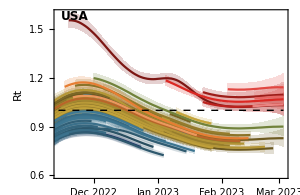
-Graphics- |

```mathematica
fig=Grid[{{countryRtPlot["USA"],legendPanel}},Spacings->{1,1},Alignment->Right]
```

```mathematica
Export["figures/"<>dataset<>"_variant-rt.png",fig,"PNG",ImageResolution->300]
```

figures/pango-countries_variant-rt.png

```mathematica
finalRts=Table[If[Length[rtGather["USA",variant]]>0,rtGather["USA",variant][[-1,2]],Null],{variant,variants}];
```

```mathematica
finalRtsLower=Table[If[Length[rtGatherLower["USA",variant]]>0,rtGatherLower["USA",variant][[-1,2]],Null],{variant,variants}];
```

```mathematica
finalRtsUpper=Table[If[Length[rtGatherUpper["USA",variant]]>0,rtGatherUpper["USA",variant][[-1,2]],Null],{variant,variants}];
```

## Prevalence

```mathematica
pData=Import["../../estimates/"<>dataset<>"/"<>dataset<>"_I-combined-"<>model<>".tsv"];
```

```mathematica
header=pData[[1]]
```

{date,location,variant,median_I_smooth,I_smooth_upper_95,I_smooth_lower_95,I_smooth_upper_80,I_smooth_lower_80,I_smooth_upper_50,I_smooth_lower_50,median_freq}

```mathematica
headerRules=MapIndexed[#1->#2[[1]]&,header]
```

{date→1,location→2,variant→3,median_I_smooth→4,I_smooth_upper_95→5,I_smooth_lower_95→6,I_smooth_upper_80→7,I_smooth_lower_80→8,I_smooth_upper_50→9,I_smooth_lower_50→10,median_freq→11}

```mathematica
pData=Drop[pData,1];
```

Only keep data points with incidence

```mathematica
pData=Cases[pData,x_/;x[[4]]>0.9];
```

```mathematica
pGather[country_,variant_]:=Cases[pData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,4}]]
```

```mathematica
pGatherLower[country_,variant_]:=Cases[pData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,8}]]
```

```mathematica
pGatherUpper[country_,variant_]:=Cases[pData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,7}]]
```

```mathematica
variantCountryPrevalencePlot[country_,variant_,color_]:=Module[{medianSeries,lowerSeries,upperSeries},
medianSeries=pGather[country,variant];
lowerSeries=pGatherLower[country,variant];
upperSeries=pGatherUpper[country,variant];
DateListLogPlot[{medianSeries,lowerSeries,upperSeries},Frame->{True,True,False,False},FrameLabel->{"","Estimated variant cases"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.65,ImagePadding->{{55,5},{15,10}},Joined->True,PlotRange->{{startDate,modelEndDate},
{200,100000}},DateTicksFormat->{"MonthNameShort"},PlotRangeClipping->True,PlotStyle->{color,None,None},FrameTicks->{{{10,20,100,200,1000,2000,10000,20000,100000,200000,1000000},Automatic},{dateTicks,Automatic}},Filling->2->{3},FillingStyle->Directive[Opacity[0.2],color],
Epilog->{Text[Style[country,Black,FontSize->12,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}]}]
]
```

```mathematica
countryPrevalencePlot[country_]:=Show[Table[variantCountryPrevalencePlot[country,variants[[i]],colors[[i]]],{i,1,n}]]
```

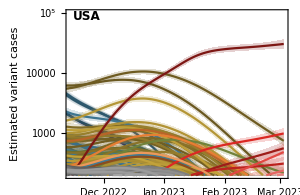
-Graphics- |

```mathematica
fig=Grid[{{countryPrevalencePlot["USA"],legendPanel}},Spacings->{1,1},Alignment->Right]
```

```mathematica
Export["figures/"<>dataset<>"_variant-estimated-log-cases.png",fig,"PNG",ImageResolution->300]
```

figures/pango-countries_variant-estimated-log-cases.png

```mathematica
variantCountryPrevalencePlot[country_,variant_,color_]:=Module[{medianSeries,lowerSeries,upperSeries},
medianSeries=pGather[country,variant];
lowerSeries=pGatherLower[country,variant];
upperSeries=pGatherUpper[country,variant];
DateListPlot[{medianSeries,lowerSeries,upperSeries},Frame->{True,True,False,False},FrameLabel->{"","Estimated variant cases"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.65,ImagePadding->{{55,5},{15,10}},Joined->True,PlotRange->{{startDate,modelEndDate},
{0,32000}},DateTicksFormat->{"MonthNameShort"},PlotRangeClipping->True,PlotStyle->{color,None,None},FrameTicks->{{Automatic,Automatic},{dateTicks,Automatic}},Filling->2->{3},FillingStyle->Directive[Opacity[0.2],color],
Epilog->{Text[Style[country,Black,FontSize->12,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}]}]
]
```

```mathematica
countryPrevalencePlot[country_]:=Show[Table[variantCountryPrevalencePlot[country,variants[[i]],colors[[i]]],{i,1,n}]]
```

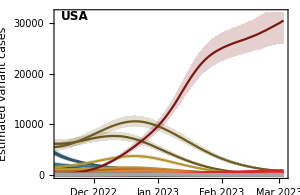
-Graphics- |

```mathematica
fig=Grid[{{countryPrevalencePlot["USA"],legendPanel}},Spacings->{1,1},Alignment->Right]
```

```mathematica
Export["figures/"<>dataset<>"_variant-estimated-cases.png",fig,"PNG",ImageResolution->300]
```

figures/pango-countries_variant-estimated-cases.png

## Frequency

```mathematica
logitTransform[x_]:=Log[x/(1-x)]
```

```mathematica
logitBackTransform[y_]:=Exp[y]/(1+ Exp[y])
```

```mathematica
logitTicks=Map[{logitTransform[#],ToString[If[#<0.01,NumberForm[Round[100*#,0.1],{3,1}],Round[100*#]]]<>"%"}&,{0.001,0.01,0.1,0.5,0.9,0.99}];
```

```mathematica
fData=Import["../../estimates/"<>dataset<>"/"<>dataset<>"_freq-combined-"<>model<>".tsv"];
```

```mathematica
header=fData[[1]]
```

{date,location,variant,median_freq,freq_upper_95,freq_lower_95,freq_upper_80,freq_lower_80,freq_upper_50,freq_lower_50}

```mathematica
headerRules=MapIndexed[#1->#2[[1]]&,header]
```

{date→1,location→2,variant→3,median_freq→4,freq_upper_95→5,freq_lower_95→6,freq_upper_80→7,freq_lower_80→8,freq_upper_50→9,freq_lower_50→10}

```mathematica
fData=Drop[fData,1];
```

```mathematica
fGather[country_,variant_]:=Cases[fData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,4}]]
```

```mathematica
fGatherLower[country_,variant_]:=Cases[fData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,8}]]
```

```mathematica
fGatherUpper[country_,variant_]:=Cases[fData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,7}]]
```

```mathematica
logitTransformDateSeries[dateSeries_]:=Map[{#[[1]],Which[#[[2]]<0.0001,logitTransform[0.0001],#[[2]]>0.9999,logitTransform[0.9999],True,logitTransform[#[[2]]]]}&,dateSeries]
```

```mathematica
variantCountryFrequencyPlot[country_,variant_,color_]:=Module[{medianSeries,lowerSeries,upperSeries},
medianSeries=logitTransformDateSeries[fGather[country,variant]];
lowerSeries=logitTransformDateSeries[fGatherLower[country,variant]];
upperSeries=logitTransformDateSeries[fGatherUpper[country,variant]];
DateListPlot[{medianSeries,lowerSeries,upperSeries},Frame->{True,True,False,False},FrameLabel->{"","Estimated variant frequency"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.65,ImagePadding->{{55,5},{15,10}},Joined->True,PlotRange->{{startDate,modelEndDate},
{logitTransform[0.0005],logitTransform[0.9]}},DateTicksFormat->{"MonthNameShort"},PlotRangeClipping->True,PlotStyle->{color,None,None},FrameTicks->{{logitTicks,Automatic},{dateTicks,Automatic}},Filling->2->{3},FillingStyle->Directive[Opacity[0.2],color],
Epilog->{Text[Style[country,Black,FontSize->12,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}]}]
]
```

```mathematica
countryFrequencyPlot[country_]:=Show[Table[variantCountryFrequencyPlot[country,variants[[i]],colors[[i]]],{i,1,n}]]
```

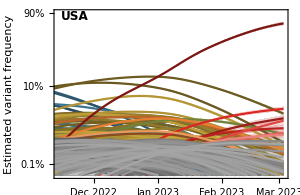
-Graphics- |

```mathematica
fig=Grid[{{countryFrequencyPlot["USA"],legendPanel}},Spacings->{1,1},Alignment->Right]
```

```mathematica
Export["figures/"<>dataset<>"_variant-estimated-frequency.png",fig,"PNG",ImageResolution->300]
```

figures/pango-countries_variant-estimated-frequency.png

```mathematica
finalFrequencies=Table[fGather["USA",variant][[-1,2]],{variant,variants}];
```

## Rts and frequencies across variants

```mathematica
pos=Flatten[Position[finalRts,x_/;NumberQ[x]]];
```

```mathematica
finalRts=finalRts[[pos]];
```

```mathematica
finalRtsLower=finalRtsLower[[pos]];
```

```mathematica
finalRtsUpper=finalRtsUpper[[pos]];
```

```mathematica
finalFrequencies=finalFrequencies[[pos]];
```

```mathematica
finalVariants=variants[[pos]];
```

```mathematica
finalColors=colors[[pos]];
```

```mathematica
points=ListPlot[Table[{{i,finalRts[[i]]}},{i,Length[finalVariants]}],PlotStyle->finalColors];
```

```mathematica
lines=ListLinePlot[Table[{{i,finalRtsLower[[i]]},{i,finalRtsUpper[[i]]}},{i,Length[finalVariants]}],PlotTheme->"FullAxes",Frame->{True,True,False,False},FrameLabel->{"","Rt"},PlotStyle->Map[Directive[Opacity[0.75],#]&,finalColors],AspectRatio->0.3,ImageSize->700,PlotRange->{rtMin,rtMax},FrameTicks->{{Automatic,Automatic},{Table[{i,Rotate[finalVariants[[i]],Pi/2]},{i,Length[finalVariants]}],Automatic}},Epilog->{Text[Style["USA",Black,FontSize->12,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}],Dashed,Black,Line[{{0,1},{n,1}}]}];
```

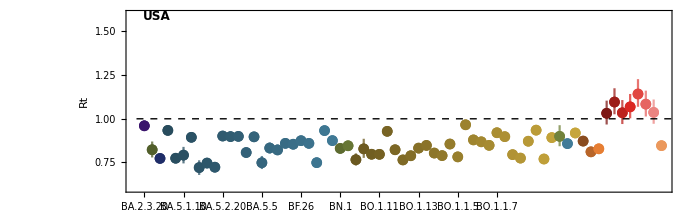

```mathematica
fig=Show[lines,points]
```

```mathematica
Export["figures/"<>dataset<>"_variant-rt-listplot.png",fig,"PNG",ImageResolution->300]
```

figures/pango-countries_variant-rt-listplot.png

```mathematica
topPos=Reverse[Ordering[finalRts,-8]];
```

```mathematica
tableValues=Table[{finalVariants[[p]],Round[finalRts[[p]],0.01],ToString[Round[finalRtsLower[[p]],0.01]]<>" - "<>ToString[Round[finalRtsUpper[[p]],0.01]]},{p,topPos}];
```

```mathematica
table=Style[TableForm[tableValues,TableHeadings->{None,{"lineage","Rt estimate","80% uncertainty interval"}},TableSpacing->{3,1}],FontFamily->"Helvetica",FontSize->12];
```

```mathematica
labels=Table[If[MemberQ[topPos,i],finalVariants[[i]],""],{i,Length[finalRts]}];
```

```mathematica
points=ListPlot[MapThread[{{#1,#2}}&,{finalFrequencies,finalRts}],PlotTheme->"FullAxes",Frame->{True,True,False,False},FrameLabel->{"Current lineage frequency","Rt"},PlotStyle->Map[Directive[Opacity[0.75],#]&,finalColors],AspectRatio->0.65,ImageSize->350,PlotRange->{{0,1},{rtMin,rtMax}},FrameTicks->{{Automatic,Automatic},{Table[{i,ToString[Round[100*i]]<>"%"},{i,0,1,0.2}],Automatic}},Epilog->{Text[Style["USA",Black,FontSize->12,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}],Dashed,Black,Line[{{0,1},{n,1}}]},PlotLabels->Placed[labels,Right]];
```

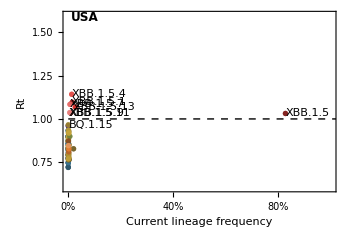
-Graphics- | lineage | Rt estimate | 80% uncertainty interval
XBB.1.5.4 | 1.14 | 1.07 - 1.23
XBB.1.5.1 | 1.1 | 1.03 - 1.17
XBB.1.5.7 | 1.08 | 1.01 - 1.16
XBB.1.5.13 | 1.07 | 1. - 1.14
XBB.1.5.9 | 1.04 | 0.97 - 1.11
XBB.1.5.11 | 1.03 | 0.97 - 1.11
XBB.1.5 | 1.03 | 0.97 - 1.1
BQ.1.15 | 0.97 | 0.94 - 0.99

```mathematica
fig=Grid[{{points,table}}]
```

```mathematica
Export["figures/"<>dataset<>"_variant-rt-top.png",fig,"PNG",ImageResolution->300]
```

figures/pango-countries_variant-rt-top.png